```mathematica
ClearAll["Global`*"]
```

```mathematica
cs=-Graphics-;
```

```mathematica
cs=-Graphics-;
```

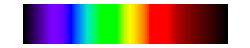
```mathematica
cs=-Graphics-;
```

```mathematica
getColmColor=Function[{cs,colmn},
csd=ImageData[cs][[;;,colmn,1;;3]];
c1r=Total[csd]/Length[csd];
{c1r,RGBColor[c1r]}
];
```

```mathematica
findλ=Function[{c1r},

col=ColorData["VisibleSpectrum"];
rang=ColorData["VisibleSpectrum","Range"];
rgbdata=Table[col[λ][[#]]&/@{1,2,3},{λ,rang[[1]],rang[[2]],0.1}];
{red,green,blue}={rgbdata[[;;,1]],rgbdata[[;;,2]],rgbdata[[;;,3]]};

redd=Flatten[Differences[{c1r[[1]],red[[#]]}]&/@Range[1,Length[red]]];
λs=#&/@Range[1,Length[red]];
λrred=Partition[Riffle[λs,redd],2];
searchred=SortBy[Abs[λrred],Last];

greend=Flatten[Differences[{c1r[[2]],green[[#]]}]&/@Range[1,Length[green]]];
λs=#&/@Range[1,Length[red]];
λrgreen=Partition[Riffle[λs,greend],2];
searchgreen=SortBy[Abs[λrgreen],Last];

blued=Flatten[Differences[{c1r[[3]],blue[[#]]}]&/@Range[1,Length[red]]];
λs=#&/@Range[1,Length[red]];
λrblue=Partition[Riffle[λs,blued],2];
searchblue=SortBy[Abs[λrblue],Last];

list={};
For[i=1,i<Length[searchred],i=i+100,
gat=Gather[Flatten[{searchred[[;;i,1]],searchgreen[[;;i,1]],searchblue[[;;i,1]]}]];
If[Max[Length[gat[[#]]]&/@Range[1,Length[gat]]]>2,
cros=Select[gat,Length[#]>2&];
colfound={red[[cros[[1,1]]]],green[[cros[[1,1]]]],blue[[cros[[1,1]]]]};
AppendTo[list,cros[[1,1]]
]
]
];
flg=Flatten[Position[c1r,Max[c1r]]][[1]];
If[flg==1,
xλ=Mean[Union[list[[1;;3]]]]*0.1+380;
];
If[flg==2,
xλ=Mean[Union[list[[2;;2]]]]*0.1+380;
];
If[flg==3,
xλ=Mean[Union[list[[1;;1]]]]*0.1+380;
];
{xλ,ColorData["VisibleSpectrum"][xλ]}
];
```

```mathematica
colrgb=getColmColor[cs,750]
findλ[colrgb[[1]]]
```

{{0.628431,0.156863,0.0857843},RGBColor[{0.6284313725490196, 0.1568627450980392, 0.0857843137254902}]}

{656.8,RGBColor[0.7382354655759746, 0., 0.]}

{{380,50},{383,5},{387,5},{390,5},{395,5},{398,5},{400,5},{406,5},{409,5},{410,5},{417,4},{420,10},{428,5},{430,25},{426,5},{450,5},{458,5},{460,5},{465,15},{468,5},{469,5},{480,5},{483,5},{486,4},{491,5},{493,5},{495,5},{499,5},{506,5},{509,5},{514,5},{520,40},{550,5},{554,5},{558,5},{561,5},{565,4},{569,5},{573,25},{574,10},{576,5},{586,5},{599,5},{609,5},{610,59},{639,5},{657,5},{658,5},{659,5},{660,5},{669,5},{670,20},{680,15},{690,14},{700,5}}

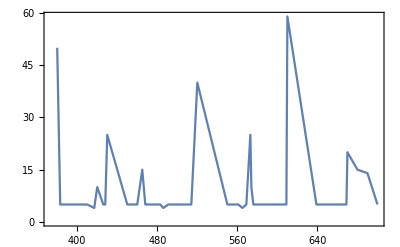

```mathematica
spectrum=findλ[getColmColor[cs,#][[1]]]&/@Range[1,ImageDimensions[cs][[1]],1];
spectr=Tally[Round[spectrum[[;;,1]]]]
ListLinePlot[SortBy[spectr,First],PlotRange->All,Frame->True]
```

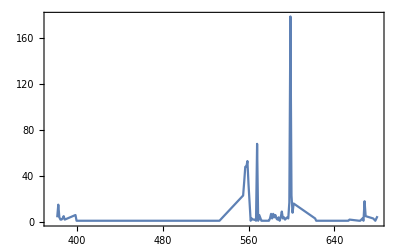

```mathematica
spectr=Tally[Round[spectrum[[;;,1]]]];
ListLinePlot[SortBy[spectr,First],PlotRange->All,Frame->True]
```